# What is the maximum entropy distribution for known μ and σ where x is positive?

Here p[x] is the maximum entropy pdf of the distribution where we know that x is non-negative and we know the mean μ and variance σ^2.  The λ terms are the lagrange multipliers.  λ0 and λ1 will be functions only of μ.  λ2 will also be a function of σ.  (μ appears in the constraint equations for λ0 and λ1.  σ appears in the λ2 constraint.

```mathematica
p[x_]:=Exp[-1+λ0+λ1 x + λ2(x-μ)^2]
```

Here, I apply the first constraint

```mathematica
totalArea=Integrate[p[x],{x,0,Infinity},Assumptions-> λ2<0&&λ1<0]
```

(ⅇ^(-1+λ0-λ1^2/(4 λ2)+λ1 μ) √π (1+Erf[(λ1-2 λ2 μ)/(2 √-λ2)]))/(2 √-λ2)

```mathematica
InputForm[totalArea]
```

(E^(-1 + λ0 - λ1^2/(4*λ2) + λ1*μ)*Sqrt[Pi]*
  (1 + Erf[(λ1 - 2*λ2*μ)/(2*Sqrt[-λ2])]))/
 (2*Sqrt[-λ2])

I don't understand why Mathematica can't solve for λ0

```mathematica
Reduce[totalArea==1,λ0,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(ⅇ^(-1+λ0-λ1^2/(4 λ2)+λ1 μ) √π (1+Erf[(λ1-2 λ2 μ)/(2 √-λ2)]))/(2 √-λ2)==1,λ0,Reals]

I helped Mathematica by replacing Erf with k so that can see that λ0 is not involved in Erf[...]

```mathematica
Reduce[(totalArea/.{Erf[_]->k})==1,λ0,Reals]
```

k>-1&&λ2<0&&λ0==(λ1^2+4 λ2-4 λ1 λ2 μ-4 λ2 Log[(-√π √-λ2-k √π √-λ2)/(2 λ2)])/(4 λ2)

Now, I make a new probability distribution expression pp by putting Erf back into the λ0 expression and then substituting it back into p

```mathematica
λ0Expanded=(λ1^2+4 λ2-4 λ1 λ2 μ-4 λ2 Log[(-√π √-λ2-k √π √-λ2)/(2 λ2)])/(4 λ2)/.{k->Erf[(λ1-2 λ2 μ)/(2 √-λ2)]}
```

(λ1^2+4 λ2-4 λ1 λ2 μ-4 λ2 Log[(-√π √-λ2-√π √-λ2 Erf[(λ1-2 λ2 μ)/(2 √-λ2)])/(2 λ2)])/(4 λ2)

```mathematica
λ0Simple=FullSimplify[λ0Expanded]
```

1+λ1^2/(4 λ2)-λ1 μ+Log[2]-Log[(√π (1+Erf[(λ1-2 λ2 μ)/(2 √-λ2)]))/(√-λ2)]

```mathematica
newPPExpr=p[x]/.{λ0->λ0Simple}
```

(2 ⅇ^(x λ1+λ1^2/(4 λ2)+λ2 (x-μ)^2-λ1 μ) √-λ2)/(√π (1+Erf[(λ1-2 λ2 μ)/(2 √-λ2)]))

```mathematica
pp[x_]:=(2 ⅇ^(x λ1+λ1^2/(4 λ2)+λ2 (x-μ)^2-λ1 μ) √-λ2)/(√π (1+Erf[(λ1-2 λ2 μ)/(2 √-λ2)]))
```

```mathematica
knownMean=Integrate[x pp[x],{x,0,Infinity},Assumptions-> λ2<0&&λ1<0]
```

-(2 ⅇ^((λ1-2 λ2 μ)^2/(4 λ2)) √-λ2+√π (λ1-2 λ2 μ) (1+ⅈ Erfi[(λ1-2 λ2 μ)/(2 √λ2)] Sign[λ1-2 λ2 μ]^2))/(2 √π λ2 (1+Erf[(λ1-2 λ2 μ)/(2 √-λ2)]))

In order for the mean to have a real value, the expression √π (λ1-2 λ2 μ) (1+ⅈ Erfi[(λ1-2 λ2 μ)/(2 √λ2)] Sign[λ1-2 λ2 μ]^2) must be real.  It can only be real if ⅈ Erfi[(λ1-2 λ2 μ)/(2 √λ2)] Sign[λ1-2 λ2 μ]^2 is also real.  This can only be real if Erfi[(λ1-2 λ2 μ)/(2 √λ2)] Sign[λ1-2 λ2 μ]^2==0.  This can, in turn, only be true if either λ1 - 2 λ2 μ==0 (which makes the squared Sign function 0) or if (λ1-2 λ2 μ)/(2 √λ2)==0, which makes Erfi 0.  Both of these are true iff λ1 - 2 λ2 μ==0.  So, this is a necessary and condition for a known real mean.

When this is substituted back into the expression, we get

```mathematica
knownRealMean=FullSimplify[knownMean,Assumptions->λ1-2 λ2 μ==0]
```

1/(√π √-λ2)

Which is much better.

```mathematica
Reduce[knownRealMean==μ,λ2,Reals]
```

μ>0&&λ2==-1/(π μ^2)

Now, we can get a new expression for the density ppp: substituting λ2==-1/(π μ^2), and λ1 - 2 λ2 μ==0 and μ > 0

```mathematica
newPPPaExpr=FullSimplify[newPPExpr,λ1-2 λ2 μ==0]
```

(2 ⅇ^(x^2 λ2) √-λ2)/(√π)

```mathematica
newPPPExpr=FullSimplify[newPPPaExpr/.λ2->-1/(π μ^2),Assumptions->x>0&&μ>0]
```

(2 ⅇ^(-x^2/(π μ^2)))/(π μ)

```mathematica
Integrate[(2 ⅇ^(-x^2/(π μ^2)))/(π μ),{x,0,Infinity},Assumptions->μ>0]
```

1

```mathematica
ppp[x_,μ_]:=If[x≥0,(2 ⅇ^(-x^2/(π μ^2)))/(π μ),0]
```

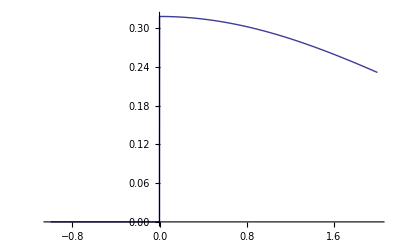

```mathematica
Plot[ppp[x,2],{x,-1,2}]
```

```mathematica
(2 ⅇ^((λ1-2 λ2 μ)^2/(4 λ2)) √-λ2+√π (λ1-2 λ2 μ) (1+ⅈ Erfi[(λ1-2 λ2 μ)/(2 √λ2)] Sign[λ1-2 λ2 μ]^2))/(2 √π λ2 (1+Erf[(λ1-2 λ2 μ)/(2 √-λ2)]))
```

```mathematica
FullSimplify[Erf[-x]]
```

-Erf[x]

```mathematica
Reduce[Im[2 ⅇ^((λ1-2 λ2 μ)^2/(4 λ2)) √-λ2]==0&&λ2≤0,{λ1,λ2,μ},Reals]
```

λ2≤0